```mathematica
(*Capacitante function parameters*)
SetDirectory[NotebookDirectory[]];
τ1 = 0.3;τ2 = 0.5;τ3 = 0.9;τ4 = 1;
C0=1;C1=0.5;T=1;
```

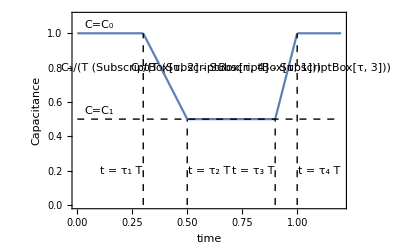

Fig2.png

```mathematica
CC[t_]=Which[t< τ1 T,C0,t<τ2 T,C0+(t/T- τ1)(C1-C0)/(τ2-τ1),t<τ3 T,C1,True,C1 + (t/T-τ3)(C0-C1)/(τ4-τ3)];
g1 = Plot[{CC[Mod[t,T]]},{t,0,1.2*T},
PlotRange->{0,1.1},
Frame->True,
FrameLabel->{"time","Capacitance"},
LabelStyle->Directive[Black,FontSize->16]
];
g2 = Graphics[{Dashed, Line[{{τ1 T,0},{τ1 T,1}}]}];
g3 = Graphics[{Text["t = τ_1 T",{τ1  T -0.1,0.2}]}];
g4 = Graphics[{Dashed, Line[{{τ2 T,0},{τ2 T,C1}}]}];
g5 = Graphics[{Text["t = τ_2 T",{τ2 T +0.1,0.2}]}];
g6 = Graphics[{Dashed, Line[{{τ3 T,0},{τ3 T,C1}}]}];
g7 = Graphics[{Text["t = τ_3 T",{τ3 T -0.1,0.2}]}];
g8 = Graphics[{Dashed, Line[{{τ4,0},{τ4,1}}]}];
g9 = Graphics[{Text["t = τ_4 T",{τ4 T+0.1,0.2}]}];

g10 = Graphics[{Text["C_1/(T (SubscriptBox[τ, 2] - SubscriptBox[τ, 1]))",{15.5/30*T,0.8}],Text["C_0/(T (SubscriptBox[τ, 4] - SubscriptBox[τ, 3]))",{25/30T,0.8}]}];
g11= Graphics[{Dashed, Line[{{0,C1},{1.2T,C1}}]}];
(*g11= Graphics[{Dashed, Line[{{0,C0},{τ2 T,C0}}]}];*)
g12 = Graphics[{Text["C=C_0",{0.1 T,1.05}]}];
g13 = Graphics[{Text["C=C_1",{0.1 T,0.55}]}];


export = Show[g1,g2,g3,g4,g5,g6,g7,g8,g9,g10,g11,g12,g13]
Export["Fig2.png",export]
```